```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Estimator Parameters: Length of Wilson Lines:*)
L:=10
(*Number of Time Steps:*)
n:=10
(*Distance between instanton and anti-instanton*)
R:=5
(*Distance between quark and anti-quark*)
r:=1
(*Integration Bounds*)
l:=20
```

```mathematica
η:=Array[Eta,{4,4,3}]
Do[Eta[k,l,a]=LeviCivitaTensor[3][[k,l,a]]
,{k,1,3},{l,1,3},{a,1,3}]
Do[Eta[4,4,a]=0,{a,1,3}]
Do[Eta[k,4,a]=KroneckerDelta[k,a],{k,1,3},{a,1,3}]
Do[Eta[4,k,a]=-KroneckerDelta[k,a],{k,1,3},{a,1,3}]
ηbar:=Array[Etabar,{4,4,3}]
Do[Etabar[k,l,a]=LeviCivitaTensor[3][[k,l,a]]
,{k,1,3},{l,1,3},{a,1,3}]
Do[Etabar[4,4,a]=0,{a,1,3}]
Do[Etabar[k,4,a]=-KroneckerDelta[k,a],{k,1,3},{a,1,3}]
Do[Etabar[4,k,a]=+KroneckerDelta[k,a],{k,1,3},{a,1,3}]
```

```mathematica
(*Define instanton solutions
Areg[γ2_,ρ_,t_]:=t/(t^2+γ2+ρ^2)
Aanti[γ2_,ρ_,t_]:=t/(t^2+γ2+ρ^2)*)
```

```mathematica
(*Instanton rotation*)
Rvec:={0,0,0,R}(*R{Sqrt[1-ct3^2]Sqrt[1-ct2^2]Sin[θ1],Sqrt[1-ct3^2]Sqrt[1-ct2^2]Cos[θ1],Sqrt[1-ct3^2]ct2,ct3}
R{Sin[θ3]Sin[θ2]Sin[θ1],Sin[θ3]Sin[θ2]Cos[θ1],Sin[θ3]Cos[θ2],Cos[θ3]}*)
Simplify[Sum[Rvec[[m]]^2,{m,1,4}]]
```

25

```mathematica
(*Ratio Ansatz*)
Ya[y_]:=y+Rvec/2
Yi[y_]:=y-Rvec/2
Arat[y_]:=Table[Sum[(ηbar[[μ,ν,aa]]*Yi[y][[ν]]*Ya[y].Ya[y]+η[[μ,ν,aa]]*Ya[y][[ν]]*Yi[y].Yi[y])/((Yi[y].Yi[y])(Ya[y].Ya[y])+Yi[y].Yi[y]+Ya[y].Ya[y]),{ν,1,4}],{μ,1,4},{aa,1,3}]
```

```mathematica
(*Wilson Line at a point along the line*)
dx:=L/n{Sin[θ3]Sin[θ2]Sin[θ1],Sin[θ3]Sin[θ2]Cos[θ1],Sin[θ3]Cos[θ2],Cos[θ3]}
adotx[a_]:=Sum[a[[μ]]dx[[μ]],{μ,1,4}]
W2[a_]:=IdentityMatrix[2]*Cos[Sqrt[adotx[a].adotx[a]]]+I*(Sum[adotx[a][[i]]/Sqrt[adotx[a].adotx[a]]PauliMatrix[i],{i,1,3}])Sin[Sqrt[adotx[a].adotx[a]]]
Wd2[a_]:=IdentityMatrix[2]*Cos[Sqrt[adotx[a].adotx[a]]]-I*(Sum[adotx[a][[i]]/Sqrt[adotx[a].adotx[a]]PauliMatrix[i],{i,1,3}])Sin[Sqrt[adotx[a].adotx[a]]]
```

```mathematica
(*Table of wilson lines along L*)
WList[y_]:=Table[W2[Arat[y+(i-1/2)dx]],{i,1,n}]
WdList[y_]:=Reverse[Table[Wd2[Arat[y+(i-1/2)dx]],{i,1,n}]]
```

```mathematica
(*Matrix Product*)
Wapprox[y_]:=Dot@@WList[y] (* applies the function to everything in the table *)
Wdapprox[y_]:=Dot@@WdList[y]
ypoint={1.,1.,0.,0};(* just example *)
```

```mathematica
(*A side by side comparison shows leaving trig in takes half the time of replacing it with algebra*)
timing1=AbsoluteTiming[Wapprox[ypoint]/.{θ3->1,θ1->0,θ2->1} ]
```

$Aborted

```mathematica
Tr[timing1[[2]].ConjugateTranspose[timing1[[2]]]]
```

2.+0. ⅈ

```mathematica
timing2=AbsoluteTiming[Wapprox[ypoint]/.{ct3->0.54,θ1->0,ct2->0.54} ]
```

```mathematica
(*Upper and Lower Lines for B fields*)
WApproxUpper[y_,t_]:=Dot@@Table[W2[Arat[y+(i-1/2)dx]],{i,t,n}]
WApproxLower[y_,t_]:=Dot@@Table[W2[Arat[y+(i-1/2)dx]],{i,1,t}]
WdApproxUpper[y_,t_]:=Dot@@Table[Wd2[Arat[y+(i-1/2)dx]],{i,t,n}]
WdApproxLower[y_,t_]:=Dot@@Table[Wd2[Arat[y+(i-1/2)dx]],{i,1,t}]
```

```mathematica
Tr[Mexample.ConjugateTranspose[Mexample]]
```

Tr[Mexample.ConjugateTranspose[Mexample]]

```mathematica
ConjugateTranspose[Wapprox[ypoint]]
Wdapprox[ypoint]
```

$Aborted

$Aborted

```mathematica
Mexample // MatrixForm
```

Mexample

```mathematica
Imes[y_,rr_]:=1-1/2*Tr[Wapprox[y].Wdapprox[y-{rr,0,0,0}]](* integrand *)
```

```mathematica
AbsoluteTiming[Imes[{-100,-100,-100,0},r]]/.{θ3->0.,θ1->0.,θ2->0.}
```

{4.47249,2.635×10^-10+0. ⅈ}

```mathematica
AbsoluteTiming[Imes[ypoint,r]/.{θ3->0,θ1->0,θ2->0}]
```

{178.461,0.623363+0. ⅈ}

```mathematica
Imes[ypoint,0]/.{θ3->1.,θ1->0,θ2->0}
```

-4.44089×10^-16+0. ⅈ

```mathematica
Integrate[Sin[θ2],{θ1,0,2Pi},{θ2,0,Pi}]
```

4 π

```mathematica
AngleDataMes=Table[{θ3,NIntegrate[1/(4Pi)Sin[θ3]^2Sin[θ2]Imes[{y1,y2,y3,0},r],{θ1,0,2Pi},{θ2,0,Pi},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal->2]},{θ3,0,Pi,Pi/20}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 11.0553-2.86931×10^-17 ⅈ and 0.0154316 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 24.0693-3.88936×10^-17 ⅈ and 0.0531174 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 43.6013-2.51677×10^-16 ⅈ and 0.143339 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{0,0.},{π/20,0.787435},{π/10,3.88977},{(3 π)/20,11.0553},{π/5,24.0693},{π/4,43.6013},{(3 π)/10,68.3098},{(7 π)/20,94.1977},{(2 π)/5,113.018},{(9 π)/20,123.434},{π/2,129.382},{(11 π)/20,123.434},{(3 π)/5,113.018},{(13 π)/20,94.1977},{(7 π)/10,68.3098},{(3 π)/4,43.6013},{(4 π)/5,24.0693},{(17 π)/20,11.0553},{(9 π)/10,3.88977},{(19 π)/20,0.787435},{π,0.}}

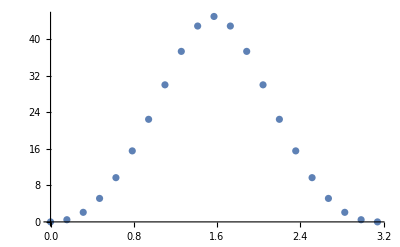

```mathematica
ListPlot[AngleDataMes]
```

```mathematica
DistanceDataMes=Table[{rr,NIntegrate[1/(2Pi^2)Sin[θ3]^2Sin[θ2]Imes[{y1,y2,y3,0},rr],{θ1,0,2Pi},{θ2,0,Pi},{θ3,0,Pi},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal->2]},{rr,0,5,0.5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 27.7369-2.93829×10^-16 ⅈ and 0.822518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 109.46-1.68981×10^-16 ⅈ and 3.08926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 241.6+1.63888×10^-15 ⅈ and 5.74218 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{0.,-3.68369×10^-11+1.03957×10^-28 ⅈ},{0.5,27.7369},{1.,109.46},{1.5,241.6},{2.,422.694},{2.5,648.349},{3.,914.378},{3.5,1216.87},{4.,1555.24},{4.5,1925.52},{5.,2323.8}}

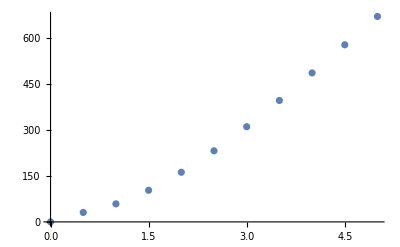

```mathematica
ListPlot[DistanceDataMes]
```

```mathematica
(*Field Strength*)
Fmunu=Table[D[Arat[{y[1],y[2],y[3],y[4]}][[mu]][[a]],y[nu] ]-D[Arat[{y[1],y[2],y[3],y[4]}][[nu]][[a]],y[mu] ],{mu,1,4},{nu,1,4},{a,1,3}]+Table[
-Sum[
LeviCivitaTensor[3][[a,b,c]]Arat[{y[1],y[2],y[3],0}][[mu]][[b]]Arat[{y[1],y[2],y[3],0}][[nu]][[c]],{b,1,3},{c,1,3}],
{mu,1,4},{nu,1,4},{a,1,3}];
B[y1_,y2_,y3_,t_]:=Table[1/2Sum[LeviCivitaTensor[3][[i]][[j]][[k]](Fmunu[[j]][[k]][[a]]/.{y[1]->y1,y[2]->y2,y[3]->y3,y[4]->t})PauliMatrix[a] ,{j,1,3},{k,1,3},{a,1,3}],{i,1,3}]
```

```mathematica
B[ypoint[[1]],ypoint[[2]],ypoint[[3]],1][[1]]/.{θ3->1.,θ1->0,θ2->0}
```

{{-0.0664156,0.0246322+0.0378125 ⅈ},{0.0246322-0.0378125 ⅈ,0.0664156}}

```mathematica
(*Integrand for two B fields*)
ImesBB[y1_,y2_,y3_,t1_,t2_]:=Sum[Tr[WApproxLower[{y1,y2,y3,0},t1].B[y1,y2,y3,t1][[i]].WApproxUpper[{y1,y2,y3,0},t1].WdApproxUpper[{y1-r,y2,y3,0},t2].B[y1,y2,y3,t1][[i]].WdApproxLower[{y1-r,y2,y3,0},t2]],{i,1,3}]
```

```mathematica
AbsoluteTiming[ImesBB[ypoint[[1]],ypoint[[2]],ypoint[[3]],1,1]/.{θ3->1.,θ1->0,θ2->0}]
```

{1701.39,0.136186+0. ⅈ}

```mathematica
AngleDataMesBB=Table[{θ3,Sum[(L/n)^2*NIntegrate[1/(2Pi^2)Sin[θ3]^2Sin[θ2]ImesBB[y1,y2,y3,t1,t2],{θ1,0,2Pi},{θ2,0,Pi},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal->2],{t1,1,n},{t2,1,n}]},{θ3,0,Pi,Pi/4}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.92062+2.09352×10^-18 ⅈ and 0.0233804 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.71502-2.1027×10^-18 ⅈ and 0.0214771 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.00101-2.31235×10^-18 ⅈ and 0.0179915 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

$Aborted

```mathematica
ListPlot[AngleDataMesBB]
```

```mathematica
(*SU(3) matrix for baryon*)
WapproxBar[y_]:=ArrayFlatten[{{Wapprox[y],0},{0,1}}]
```

```mathematica
Sum[LeviCivitaTensor[3][[b1]][[b2]][[b3]]LeviCivitaTensor[3][[c1]][[c2]][[c3]]w1[b1,c1]w2[b2,c2]KroneckerDelta[b3,c3],{b1,1,3},{b2,1,3},{b3,1,3},{c1,1,3},{c2,1,3},{c3,1,3}]
```

w1[2,2] w2[1,1]+w1[3,3] w2[1,1]-w1[2,1] w2[1,2]-w1[3,1] w2[1,3]-w1[1,2] w2[2,1]+w1[1,1] w2[2,2]+w1[3,3] w2[2,2]-w1[3,2] w2[2,3]-w1[1,3] w2[3,1]-w1[2,3] w2[3,2]+w1[1,1] w2[3,3]+w1[2,2] w2[3,3]

```mathematica
(*Baryon Integrand-Direct Triangle*)
Ibar[y_,rr_]:=(*(WapproxBar[y][[2]][[2]]WapproxBar[y-{rr,0,0,0}][[1]][[1]]+
(*WapproxBar[y][[3]][[3]]*)WapproxBar[y-{rr,0,0,0}][[1]][[1]]-
WapproxBar[y][[2]][[1]]WapproxBar[y-{rr,0,0,0}][[1]][[2]](*-
WapproxBar[y][[3]][[1]]WapproxBar[y-{rr,0,0,0}][[1]][[3]]*)-
WapproxBar[y][[1]][[2]]WapproxBar[y-{rr,0,0,0}][[2]][[1]]+
WapproxBar[y][[1]][[1]]WapproxBar[y-{rr,0,0,0}][[2]][[2]]+
(*WapproxBar[y][[3]][[3]]*)WapproxBar[y-{rr,0,0,0}][[2]][[2]](*-
WapproxBar[y][[3]][[2]]WapproxBar[y-{rr,0,0,0}][[2]][[3]]-
WapproxBar[y][[3]][[1]]WapproxBar[y-{rr,0,0,0}][[1]][[3]]-
WapproxBar[y][[2]][[3]]WapproxBar[y-{rr,0,0,0}][[3]][[2]]*)+
WapproxBar[y][[1]][[1]](*WapproxBar[y-{rr,0,0,0}][[3]][[3]]*)+
WapproxBar[y][[2]][[2]](*WapproxBar[y-{rr,0,0,0}][[3]][[3]]*)
)*)
1+1/6(LeviCivitaTensor[3].WapproxBar[y][[1]].WapproxBar[y-{rr,0,0,0}][[2]].WapproxBar[y-{0,rr,0,0}][[3]]+
LeviCivitaTensor[3].WapproxBar[y][[3]].WapproxBar[y-{rr,0,0,0}][[1]].WapproxBar[y-{0,rr,0,0}][[2]]+LeviCivitaTensor[3].WapproxBar[y][[2]].WapproxBar[y-{rr,0,0,0}][[3]].WapproxBar[y-{0,rr,0,0}][[1]]-
LeviCivitaTensor[3].WapproxBar[y][[1]].WapproxBar[y-{rr,0,0,0}][[3]].WapproxBar[y-{0,rr,0,0}][[2]]-
LeviCivitaTensor[3].WapproxBar[y][[2]].WapproxBar[y-{rr,0,0,0}][[1]].WapproxBar[y-{0,rr,0,0}][[3]]-LeviCivitaTensor[3].WapproxBar[y][[3]].WapproxBar[y-{rr,0,0,0}][[2]].WapproxBar[y-{0,rr,0,0}][[1]])
```

```mathematica
AbsoluteTiming[Ibar[ypoint,0]/.{θ3->1.,θ1->0,θ2->0}]
```

{1346.47,2.+0. ⅈ}

```mathematica
AbsoluteTiming[Ibar[{100,100,100,0},r]/.{θ3->1.,θ1->0,θ2->0}]
```

{74.1574,5.97626+0. ⅈ}

```mathematica
AbsoluteTiming[Ibar2[ypoint]/.{θ3->1.,θ1->0,θ2->0}]
```

{280.352,1.-0.0825364 ⅈ}

```mathematica
AngleDataBar=Table[{θ3,NIntegrate[1/(2Pi^2)Sin[θ3]^2Sin[θ2]Ibar[{y1,y2,y3,0},r],{θ1,0,2Pi},{θ2,0,Pi},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal->2]},{θ3,0,Pi,Pi/20}]
```

NIntegrate::inumr: The integrand (Ibar[{y1,y2,y3,0},1] Sin[π/20]^2 Sin[θ2])/(2 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{-20,20},{-20,20},{-20,20}}.

NIntegrate::inumr: The integrand ((-1+√5)^2 Ibar[{y1,y2,y3,0},1] Sin[θ2])/(32 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{-20,20},{-20,20},{-20,20}}.

NIntegrate::inumr: The integrand (Ibar[{y1,y2,y3,0},1] Sin[(3 π)/20]^2 Sin[θ2])/(2 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{-20,20},{-20,20},{-20,20}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0,0.},{π/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{π/10,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(3 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{π/5,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{π/4,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(3 π)/10,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(7 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(2 π)/5,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(9 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{π/2,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(11 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(3 π)/5,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(13 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(7 π)/10,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(3 π)/4,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(4 π)/5,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(17 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(9 π)/10,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(19 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{π,0.}}

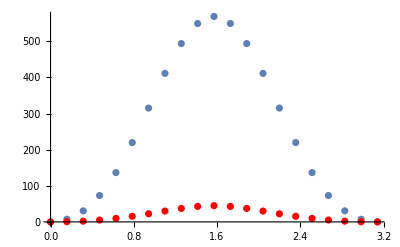

```mathematica
Show[ListPlot[AngleDataBar],ListPlot[AngleDataMes, PlotStyle->Red]]
```

```mathematica
DistanceDataBar=Table[{rr,NIntegrate[1/(2Pi^2)Sin[θ3]^2Sin[θ2]Ibar[{y1,y2,y3,0},rr],{θ1,0,2Pi},{θ2,0,Pi},{θ3,0,Pi},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal->2]},{rr,0,5,0.5}]
```

NIntegrate::inumr: The integrand (Ibar[{y1,y2,y3,0},0.] Sin[θ2] Sin[θ3]^2)/(2 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{0,3.14159},{-20,20},{-20,20},{-20,20}}.

NIntegrate::inumr: The integrand (Ibar[{y1,y2,y3,0},0.5] Sin[θ2] Sin[θ3]^2)/(2 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{0,3.14159},{-20,20},{-20,20},{-20,20}}.

NIntegrate::inumr: The integrand (Ibar[{y1,y2,y3,0},1.] Sin[θ2] Sin[θ3]^2)/(2 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{0,3.14159},{-20,20},{-20,20},{-20,20}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0.,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},rr])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{θ3,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{0.5,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},rr])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{θ3,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{1.,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},rr])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{θ3,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{1.5,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},rr])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{θ3,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{2.,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},rr])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{θ3,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{2.5,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},rr])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{θ3,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{3.,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},rr])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{θ3,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{3.5,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},rr])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{θ3,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{4.,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},rr])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{θ3,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{4.5,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},rr])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{θ3,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{5.,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},rr])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{θ3,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]}}

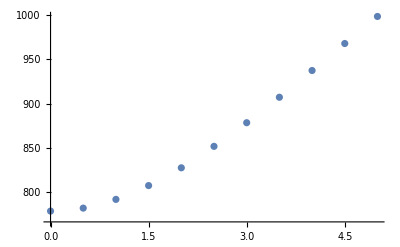

```mathematica
ListPlot[DistanceDataBar]
```

```mathematica
Show[ListPlot[DistanceDataBar],ListPlot[DistanceDataMes, PlotStyle->Red]]
```

-Graphics-